```mathematica
SetOptions[Plot3D,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[ListPlot,AspectRatio->3/4,AxesStyle->Thickness[0.002],BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[Plot,AspectRatio->3/4,AxesStyle->Thickness[0.002],BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[VectorPlot,AxesStyle->Thickness[0.002],BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[ParametricPlot3D,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[RegionPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[Histogram,AspectRatio->3/4,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[DiscretePlot,AspectRatio->3/4,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[BarChart,AspectRatio->3/4,BaseStyle->{FontFamily->"Helvetica",FontSize->18}];
SetOptions[DiscretePlot3D,AspectRatio->3/4,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[ListContourPlot,AspectRatio->3/4,BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[Histogram3D,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[DensityHistogram,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[ListLinePlot,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[LogLinearPlot,AspectRatio->3/4,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
SetOptions[LogPlot,AspectRatio->3/4,AxesStyle->Thickness[0.002],
BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
```

```mathematica
SetDirectory["/Users/doug/Box sync/Teaching/Bootcamp/"]
```

/Users/doug/Box Sync/Teaching/Bootcamp

```mathematica
MatrixForm[FileNames[]]
```

(BootcampSyllabus-2015aug26-DB.docx
Day 2
Day 3
Day 4
.DS_Store
Fitting
Fitting_092315 copy.nb
Fitting_092315.nb
Fitting_100316.nb
Mathematica notes 012814.pdf
meltdata.txt
melterrors.nb
melterrors.txt
Plotting Day 2.pdf
prettyplot2015.nb
Problems
randomnumbers.txt
Stats notebook.nb)

```mathematica
Directory[]
```

/Users/doug/Box Sync/Teaching/Bootcamp

```mathematica
data=Import["meltdata.txt","Table"]
```

{{0.,1.0122},{0.2,0.989208},{0.4,0.982287},{0.6,0.993604},{0.8,0.971504},{1.,0.989611},{1.2,0.971141},{1.4,0.966314},{1.6,0.959912},{1.8,0.977182},{2.,0.941057},{2.2,0.914023},{2.4,0.874633},{2.6,0.82663},{2.8,0.747744},{3.,0.671012},{3.2,0.556258},{3.4,0.474274},{3.6,0.427468},{3.8,0.398626},{4.,0.370593},{4.2,0.372687},{4.4,0.384226},{4.6,0.352845},{4.8,0.380133},{5.,0.352692},{5.2,0.344179},{5.4,0.345778},{5.6,0.338935},{5.8,0.337662},{6.,0.352213},{6.2,0.345807},{6.4,0.350167},{6.6,0.329048},{6.8,0.328964},{7.,0.345723},{7.2,0.330925},{7.4,0.34146},{7.6,0.333018},{7.8,0.314782},{8.,0.316627}}

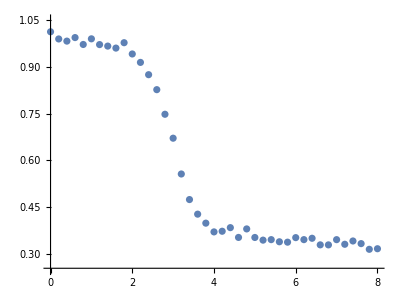

```mathematica
dataplot=ListPlot[data,PlotRange->{0.25,1.05}]
```

```mathematica
R=0.001987;
T=293.15;
dg=dgh2o+m*urea;
k=Exp[-dg/(R*T)];
fn=k/(1+k);
fd=1/(1+k);
yn=an+bn*urea;
yd=ad+bd*urea;
yobs=fn*yn+fd*yd;
```

```mathematica
myfit=NonlinearModelFit[data,yobs,
{
{an,1},
{bn,-0.02},
{ad,0.4},
{bd,-0.02},
{dgh2o,-6},
{m,2}
},
urea]
```

FittedModel[(ⅇ^(«1») («19»-«1»))/(1+ⅇ^(«1»))+(«20»«1»«1»)/(1+«1»)]

```mathematica
Normal[myfit]
```

(ⅇ^(1.71677 (6.0144-2.00881 urea)) (1.00083-0.021123 urea))/(1+ⅇ^(1.71677 (6.0144-2.00881 urea)))+(0.406918-0.0104374 urea)/(1+ⅇ^(1.71677 (6.0144-2.00881 urea)))

```mathematica
myfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
an | 1.00083 | 0.0059734 | 167.548 | 1.96752×10^-52
bn | -0.021123 | 0.005502 | -3.83914 | 0.000495871
ad | 0.406918 | 0.0125107 | 32.5255 | 9.5376×10^-28
bd | -0.0104374 | 0.00201324 | -5.18439 | 9.18337×10^-6
dgh2o | -6.0144 | 0.32459 | -18.5292 | 1.13529×10^-19
m | 2.00881 | 0.104069 | 19.3026 | 3.0725×10^-20

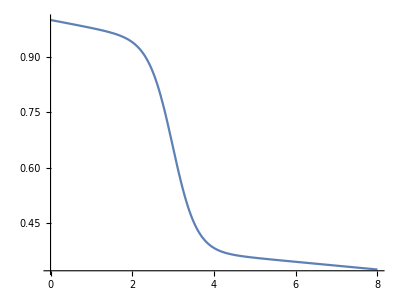

```mathematica
fitplot=Plot[myfit[urea],{urea,0,8}]
```

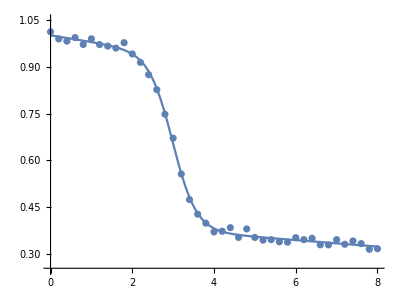

```mathematica
Show[dataplot,fitplot]
```